## Setup

```mathematica
Clear@Evaluate[Context[]<>"*"]
SetDirectory@NotebookDirectory[];
```

```mathematica
<<"Definitions/IO.wl"
```

## Equation and functions

```mathematica
<<"Definitions/Teukolsky.wl"
<<"Definitions/Eigenvalues.wl"
```

```mathematica
Eq=EqRadial/.RuleKRadial;
```

## Parameter rules and equation simplification

```mathematica
RuleR={R->Function[x,(x/τ)^(-s-ⅈ χ/τ)f[x]]};
OrdBdr=5;
RuleF={f->Function[x,∑_(n=0)^OrdBdr 𝒶[n] x^n]};
RuleBoundaryBHole={𝒶[0]->1};
EquationF=PowerExpand@Simplify[(x/τ)^(s+ⅈ χ/τ)x (x+τ) (Eq/.RuleR)];
RuleParams={τ->(2 √(1-𝒥^2))/(1+√(1-𝒥^2)),Ω̄->𝒥/2,χ->(ω̄-m Ω̄) (2-τ),rp->1+√(1-𝒥^2),ℬ->Sqrt[𝔈^2-4((𝒥 ω̄)/rp)^2+4m (𝒥 ω̄)/rp],  
λ->((𝒥 ω̄)/rp)^2-2m((𝒥 ω̄)/rp)+𝔈-s(s+1)};
RuleEigenParamCoef={𝔈->(EigenCoef/.Ruleκpm).Table[((𝒥 ω̄)/rp)^(n-1),{n,Length@EigenCoef}]+s(s+1)};
RuleEigenParamLeaver={𝔈->EigenLeaver[s,l,m,(𝒥 ω̄)/rp]+s(s+1)};
RuleAllParams=RuleParams~Join~RuleEigenParamLeaver;
```

```mathematica
ReplaceParams[𝓈_,ℓ_,𝓂_,𝒿_]:=PowerExpand[#1//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿}]&;
ReplaceParams[𝓈_,ℓ_,𝓂_,𝒿_,𝓌_]:=PowerExpand[#1//.RuleAllParams/.{s->𝓈,l->ℓ,m->𝓂,𝒥->𝒿,ω̄->𝓌}]&;
```

## Equation solver definition

```mathematica
x0=10^-14.;
xM:=4000/ω̄;
Omega=Range[0.001,0.55,0.004];
Spin={0.2,0.4,0.6,0.8,0.9,0.99,0.999};
```

```mathematica
ClearAll@SolveωF;
SolveωF[𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝒿:{__?NumberQ}|𝒿_?NumberQ]:=SolveωF[𝓈,ℓ,𝓂,𝒿,Range[0.001,0.55,0.004]]
SolveωF[𝓈_?IntegerQ,ℓ_?IntegerQ,𝓂_?IntegerQ,𝒿:{__?NumberQ}|𝒿_?NumberQ,{omega__?NumberQ}]/;And@@Thread[0<𝒿<1]&&Abs[𝓈]==1&&ℓ≥Max[Abs[𝓈],Abs[𝓂]]:=
(Block[{CoefList,SolCoef,SolFInf,eqF,ωlist,delω},
Print["𝓈 = ",𝓈,"; 𝒥 = ",#1];
{eqF,delω}=ReplaceParams[𝓈,𝓂,ℓ,#1][{EquationF,m Ω̄}];
ωlist=DeleteCases[{omega},delω];CoefList=CoefficientList[eqF/.RuleF,x]⟦;;nCoef+1⟧;SolCoef=Chop@First@Solve[CoefList==0,Table[𝒶[n],{n,1,nCoef}]//Evaluate];SolFInf=ParallelTable[f[xM]/.First@NDSolve[{eqF==0,{f[x0],f'[x0]}==({f[x0],f'[x0]}/.RuleF/.SolCoef/.RuleBoundaryBHole)},f,{x,x0,xM}],{ω̄,ωlist}];
{ConstantArray[#1,Length@ωlist],ωlist,SolFInf}ᵀ
]&)/@Flatten[{𝒿}]//Flatten[#,1]&;
```

## Start calculation and export data

```mathematica
SolωF0=SolveωF[1,1,1,Spin,Omega];
```

𝓈 = 1; 𝒥 = 0.2

𝓈 = 1; 𝒥 = 0.4

𝓈 = 1; 𝒥 = 0.6

𝓈 = 1; 𝒥 = 0.8

𝓈 = 1; 𝒥 = 0.9

𝓈 = 1; 𝒥 = 0.99

𝓈 = 1; 𝒥 = 0.999

```mathematica
SolωF2=SolveωF[-1,1,1,Spin,Omega];
```

𝓈 = -1; 𝒥 = 0.2

𝓈 = -1; 𝒥 = 0.4

𝓈 = -1; 𝒥 = 0.6

𝓈 = -1; 𝒥 = 0.8

𝓈 = -1; 𝒥 = 0.9

𝓈 = -1; 𝒥 = 0.99

𝓈 = -1; 𝒥 = 0.999

```mathematica
Data0=({#1,#2,-(ω̄ τ^2/χ)/Abs[#3]^2,#3}//ReplaceParams[1,1,1,#1,#2])&@@@SolωF0;
Export[GetZFile[1,1,1,"Leaver"],Data0];
```

```mathematica
Data2=({#1,#2,-1/(1+(ℬ^2 τ^6 Abs[#3]^2)/(rp^2 ω̄ χ(τ^2+χ^2))),#3}//ReplaceParams[-1,1,1,#1,#2])&@@@SolωF2;
Export[GetZFile[-1,1,1,"Leaver"],Data2];
```

## Edit exported data

```mathematica
OldData2=Import[GetZFile[-1,1,1,"Leaver"]];
```

```mathematica
NewData2=({#1,#2,-1/(1+(ℬ^2 τ^6 Abs[#4]^2)/(rp^2 ω̄ χ(τ^2+χ^2))),#4}//ReplaceParams[-1,1,1,#1,#2])&@@@OldData2
```

```mathematica
Export[GetZFile[-1,1,1,"Leaver"],NewData2];
Clear[OldData2,NewData2]
```

## Compare with other Brito el al. data

```mathematica
ZBCP=GroupBy[{N@Round[#1,10^-3.],#2(1+Sqrt[1-#1^2]),#3}&@@@Import@GetZFileBCP[-1,1,1]//DeleteCases[#,{𝒿_,ω_,_}/;ω>0.6𝒿]&,First->(Drop[#,1]&)];
```

Compare s=1 data

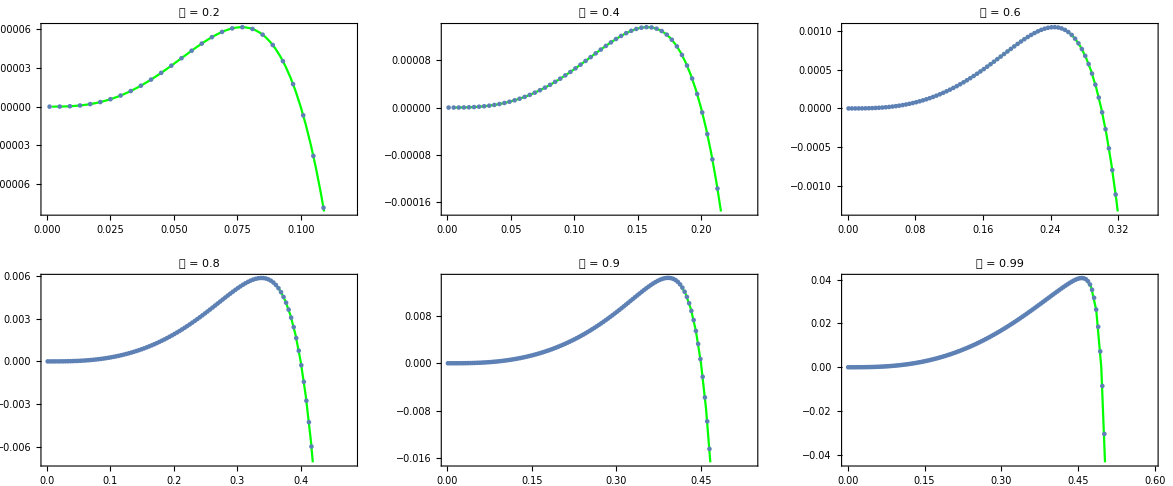

```mathematica
Z0=GroupBy[Take[#,3]&/@Import@GetZFile[1,1,1,"Leaver"],First->(Drop[#,1]&)];
Show[
ListPlot[ZBCP[#],Joined->True,PlotStyle->Green],
ListPlot[Z0[#]],
ImageSize->Medium,PlotLabel->StringRiffle[{"𝒥","=",#}," "],Frame->True
]&/@Intersection[Keys@ZBCP,Keys@Z0]//GraphicsGrid@Partition[#,3,3,1,{}]&
```

Compare s=-1 data

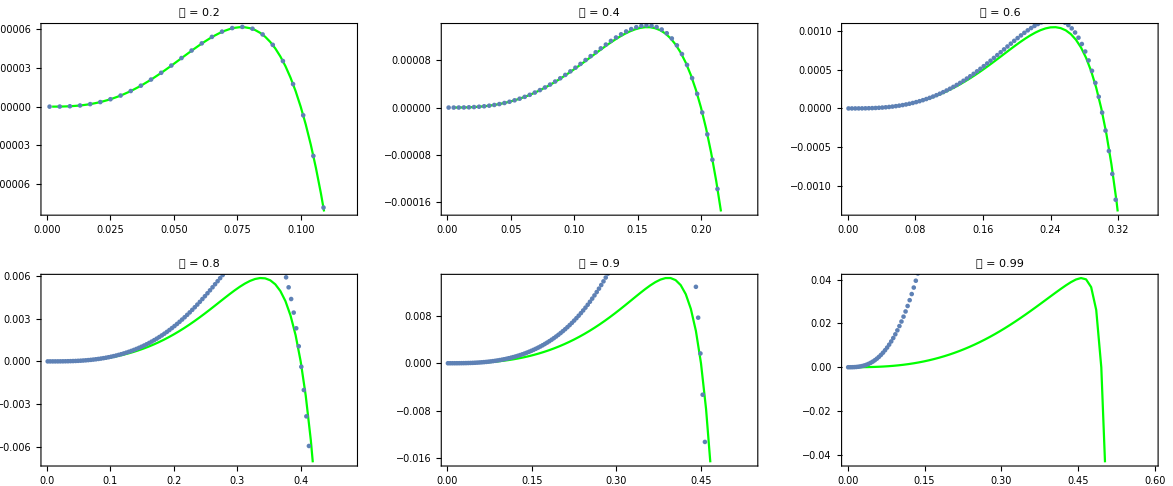

```mathematica
Z2=GroupBy[Take[#,3]&/@Import@GetZFile[-1,1,1,"Leaver"],First->(Drop[#,1]&)];
Show[
ListPlot[ZBCP[#],Joined->True,PlotStyle->Green],
ListPlot[Z2[#]],
ImageSize->Medium,PlotLabel->StringRiffle[{"𝒥","=",#}," "],Frame->True
]&/@Intersection[Keys@ZBCP,Keys@Z0]//GraphicsGrid@Partition[#,3,3,1,{}]&
```